```mathematica
chromis = Get["d:\\chroms.m"]
```

<|-6 x+11 x^2-6 x^3+x^4→1,18 x-39 x^2+29 x^3-9 x^4+x^5→2,-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→3,-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6→4,1272,-835254 x+3922089 x^2-8329039 x^3+10659594 x^4-9217413 x^5+5709061 x^6-2614472 x^7+898932 x^8-232658 x^9+44870 x^10-6280 x^11+605 x^12-36 x^13+x^14→1277,-1060230 x+4821775 x^2-9907962 x^3+12277118 x^4-10297598 x^5+6204488 x^6-2774107 x^7+935136 x^8-238331 x^9+45456 x^10-6316 x^11+606 x^12-36 x^13+x^14→1278,-825966 x+3879969 x^2-8243539 x^3+10556911 x^4-9136574 x^5+5665501 x^6-2598217 x^7+894787 x^8-231967 x^9+44802 x^10-6277 x^11+605 x^12-36 x^13+x^14→1279|>
 |  |  |  |

```mathematica
KeySort[chromis]
```

<|-6 x+11 x^2-6 x^3+x^4→1,18 x-39 x^2+29 x^3-9 x^4+x^5→2,-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→3,-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6→4,1264,-799524 x+3782502 x^2-8095440 x^3+10440859 x^4-9094046 x^5+5669003 x^6-2609807 x^7+900724 x^8-233613 x^9+45073 x^10-6302 x^11+606 x^12-36 x^13+x^14→745,-779466 x+3701605 x^2-7953028 x^3+10295806 x^4-8998950 x^5+5626926 x^6-2597043 x^7+898095 x^8-233260 x^9+45045 x^10-6301 x^11+606 x^12-36 x^13+x^14→742,-791634 x+3749947 x^2-8036163 x^3+10377517 x^4-9049718 x^5+5647649 x^6-2602607 x^7+899043 x^8-233353 x^9+45049 x^10-6301 x^11+606 x^12-36 x^13+x^14→1047|>
 |  |  |  |

```mathematica
LucesBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = LucasL[pos,x];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
EulerBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = EulerE[pos,x];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
TableForm[Map[2*EulerBaseCoeff[#]&,Select[Keys[chromis],(#/.x->3)≠0&]],TableDepth->3]
```

0 | -53 | 140 | -142 | 71 | -18 | 2 |  |  |  |  |  |  |  | 
0 | -607 | 1873 | -2388 | 1670 | -706 | 184 | -28 | 2 |  |  |  |  |  | 
0 | 1927 | -6476 | 9219 | -7397 | 3717 | -1217 | 258 | -33 | 2 |  |  |  |  | 
0 | -7109 | 25422 | -39183 | 34715 | -19745 | 7573 | -1986 | 349 | -38 | 2 |  |  |  | 
0 | -6057 | 22282 | -35374 | 32242 | -18816 | 7378 | -1968 | 349 | -38 | 2 |  |  |  | 
0 | 20621 | -80893 | 139076 | -139598 | 91483 | -41287 | 13128 | -2938 | 449 | -43 | 2 |  |  | 
0 | 25741 | -97597 | 161918 | -156987 | 99643 | -43723 | 13580 | -2985 | 451 | -43 | 2 |  |  | 
0 | -64205 | 271398 | -509485 | 565817 | -416211 | 214477 | -79614 | 21477 | -4170 | 562 | -48 | 2 |  | 
0 | -89191 | 360107 | -644495 | 683068 | -480987 | 238329 | -85522 | 22433 | -4262 | 566 | -48 | 2 |  | 
0 | -80183 | 329283 | -599777 | 646529 | -462319 | 232133 | -84198 | 22264 | -4252 | 566 | -48 | 2 |  | 
0 | -70851 | 296803 | -551768 | 606536 | -441482 | 225078 | -82660 | 22064 | -4240 | 566 | -48 | 2 |  | 
0 | -57011 | 246695 | -474228 | 538575 | -404052 | 211596 | -79500 | 21615 | -4210 | 566 | -48 | 2 |  | 
0 | 234775 | -1045198 | 2087898 | -2494800 | 1999160 | -1138695 | 475624 | -147790 | 34180 | -5795 | 692 | -53 | 2 | 
0 | 280575 | -1220014 | 2378572 | -2775200 | 2174535 | -1213626 | 497952 | -152406 | 34817 | -5848 | 694 | -53 | 2 | 
0 | 217199 | -978450 | 1978206 | -2391180 | 1936456 | -1113191 | 468560 | -146486 | 34032 | -5787 | 692 | -53 | 2 | 
0 | 322703 | -1372906 | 2617316 | -2988603 | 2296269 | -1260094 | 509952 | -154449 | 35027 | -5858 | 694 | -53 | 2 | 
0 | 199011 | -908090 | 1860181 | -2277250 | 1865973 | -1083876 | 460254 | -144917 | 33850 | -5777 | 692 | -53 | 2 | 
0 | 263935 | -1158534 | 2280504 | -2685344 | 2121779 | -1192792 | 492344 | -151398 | 34705 | -5842 | 694 | -53 | 2 | 
0 | -673039 | 3240237 | -7067736 | 9304501 | -8289253 | 5301102 | -2515072 | 900840 | -245053 | 50376 | -7678 | 831 | -58 | 2
0 | -816961 | 3848520 | -8209059 | 10570488 | -9218386 | 5778109 | -2691150 | 947963 | -254101 | 51576 | -7778 | 835 | -58 | 2
0 | -898077 | 4172996 | -8777782 | 11151404 | -9604663 | 5954348 | -2747556 | 960600 | -256019 | 51756 | -7786 | 835 | -58 | 2
0 | -844271 | 3946921 | -8354628 | 10680902 | -9256554 | 5773077 | -2679252 | 941813 | -252282 | 51237 | -7740 | 833 | -58 | 2
0 | -1129437 | 5075684 | -10318288 | 12682799 | -10596064 | 6395099 | -2885148 | 990699 | -260486 | 52167 | -7804 | 835 | -58 | 2

```mathematica
FactorInteger[1999160]
```

{{2,3},{5,1},{23,1},{41,1},{53,1}}

```mathematica
Table[LucasL[k,x],{k,1,10}]
```

{x,2+x^2,3 x+x^3,2+4 x^2+x^4,5 x+5 x^3+x^5,2+9 x^2+6 x^4+x^6,7 x+14 x^3+7 x^5+x^7,2+16 x^2+20 x^4+8 x^6+x^8,9 x+30 x^3+27 x^5+9 x^7+x^9,2+25 x^2+50 x^4+35 x^6+10 x^8+x^10}

```mathematica
Table[Fibonacci[k,x],{k,1,10}]
```

{1,x,1+x^2,2 x+x^3,1+3 x^2+x^4,3 x+4 x^3+x^5,1+6 x^2+5 x^4+x^6,4 x+10 x^3+6 x^5+x^7,1+10 x^2+15 x^4+7 x^6+x^8,5 x+20 x^3+21 x^5+8 x^7+x^9}

```mathematica
TableForm[Map[CycleBaseCoeff[#]&,Select[Keys[chromis],(#/.x->3)≠0&]],TableDepth->3]
```

0 | 0 | -14 | -5 | 13 | -6 | 1 |  |  |  |  |  |  |  | 
0 | 0 | -119 | 44 | 75 | -91 | 43 | -10 | 1 |  |  |  |  |  | 
0 | 0 | 308 | -207 | -118 | 264 | -178 | 63 | -12 | 1 |  |  |  |  | 
0 | 0 | -968 | 822 | 168 | -830 | 710 | -325 | 89 | -14 | 1 |  |  |  | 
0 | 0 | -748 | 741 | 14 | -658 | 644 | -316 | 89 | -14 | 1 |  |  |  | 
0 | 0 | 2107 | -2492 | 562 | 1668 | -2153 | 1333 | -500 | 117 | -16 | 1 |  |  | 
0 | 0 | 2983 | -3028 | 153 | 2423 | -2601 | 1465 | -519 | 118 | -16 | 1 |  |  | 
0 | 0 | -5082 | 7315 | -3569 | -3006 | 6155 | -4887 | 2346 | -735 | 149 | -18 | 1 |  | 
0 | 0 | -8513 | 10305 | -2964 | -6056 | 8708 | -5989 | 2617 | -771 | 151 | -18 | 1 |  | 
0 | 0 | -7153 | 9249 | -3376 | -4833 | 7822 | -5665 | 2555 | -766 | 151 | -18 | 1 |  | 
0 | 0 | -5817 | 8098 | -3677 | -3597 | 6860 | -5296 | 2482 | -760 | 151 | -18 | 1 |  | 
0 | 0 | -4061 | 6326 | -3750 | -1962 | 5334 | -4614 | 2325 | -745 | 151 | -18 | 1 |  | 
0 | 0 | 15506 | -24676 | 15815 | 5582 | -19616 | 18663 | -10619 | 4060 | -1066 | 187 | -20 | 1 | 
0 | 0 | 20594 | -30278 | 16513 | 9846 | -24465 | 21390 | -11535 | 4246 | -1087 | 188 | -20 | 1 | 
0 | 0 | 13566 | -22426 | 15488 | 3862 | -17672 | 17619 | -10300 | 4006 | -1062 | 187 | -20 | 1 | 
0 | 0 | 26006 | -35466 | 16094 | 14682 | -28904 | 23454 | -12084 | 4326 | -1092 | 188 | -20 | 1 | 
0 | 0 | 11686 | -20105 | 14955 | 2240 | -15639 | 16454 | -9925 | 3940 | -1057 | 187 | -20 | 1 | 
0 | 0 | 18570 | -28194 | 16503 | 8041 | -22686 | 20512 | -11283 | 4205 | -1084 | 188 | -20 | 1 | 
0 | 0 | -31955 | 60672 | -54339 | 6579 | 41171 | -54251 | 38748 | -18438 | 6147 | -1437 | 227 | -22 | 1
0 | 0 | -43338 | 77022 | -62370 | -104 | 54992 | -65252 | 44014 | -20072 | 6472 | -1475 | 229 | -22 | 1
0 | 0 | -50974 | 86947 | -65594 | -6003 | 63616 | -70881 | 46182 | -20581 | 6540 | -1479 | 229 | -22 | 1
0 | 0 | -46519 | 80944 | -62952 | -3360 | 58587 | -66914 | 44248 | -19955 | 6407 | -1462 | 228 | -22 | 1
0 | 0 | -74926 | 115195 | -71582 | -25377 | 88030 | -85644 | 51552 | -21787 | 6696 | -1488 | 229 | -22 | 1

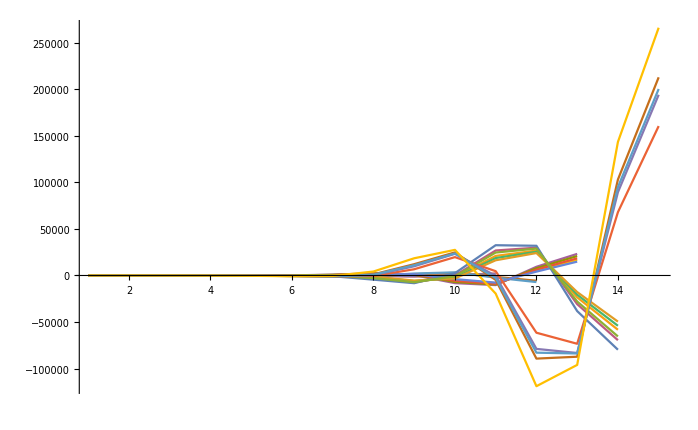

```mathematica
ListLinePlot[ Map[FourierDCT[ PathBaseCoeff[#]]&,Select[Keys[chromis],(#/.x->3)≠0&]],PlotRange->All]
```

```mathematica
Keys[chromis]
```

{-6 x+11 x^2-6 x^3+x^4,18 x-39 x^2+29 x^3-9 x^4+x^5,-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6,-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6,1264,-1393440 x+6064220 x^2-11910622 x^3+14132150 x^4-11398285 x^5+6643784 x^6-2894016 x^7+957314 x^8-240999 x^9+45645 x^10-6322 x^11+606 x^12-36 x^13+x^14,-1147926 x+5154037 x^2-10452867 x^3+12790891 x^4-10607922 x^5+6330584 x^6-2809178 x^7+941761 x^8-239149 x^9+45516 x^10-6318 x^11+606 x^12-36 x^13+x^14,-1168974 x+5230113 x^2-10569037 x^3+12888982 x^4-10657461 x^5+6345189 x^6-2811097 x^7+941563 x^8-239030 x^9+45498 x^10-6317 x^11+606 x^12-36 x^13+x^14}
 |  |  |  |

```mathematica
With[
{size=4},
Select[Table[k,{k,StartMpg[[size]],EndMPG[[size]]}],ChromaticPolynomial[ReadGrof[#],3]>0&]
]
```

{21}

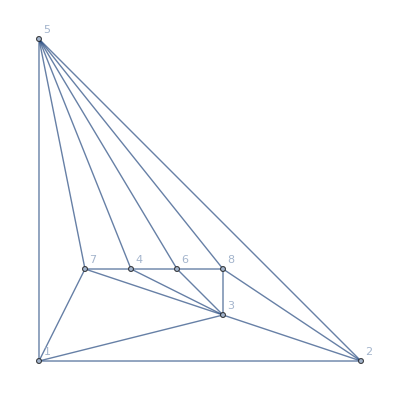

```mathematica
Graph[ReadGrof[21],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

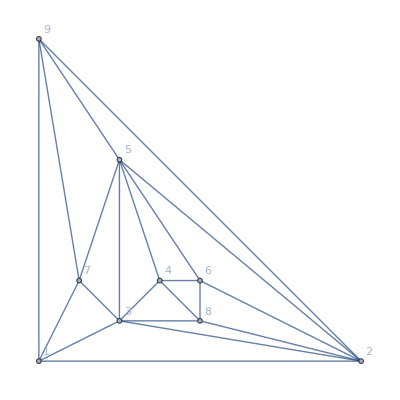

```mathematica
Graph[ReadGrof[62],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

```mathematica
With[
{size=6},
Select[Table[k,{k,StartMpg[[size]],EndMPG[[size]]}],ChromaticPolynomial[ReadGrof[#],3]>0&]
]
```

{233,305}

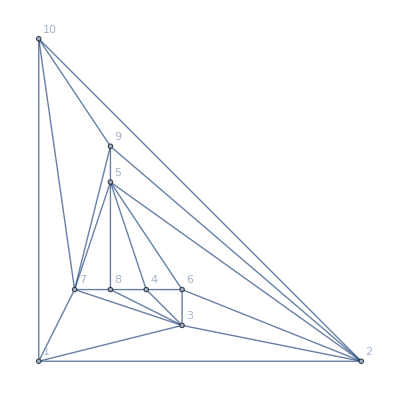

```mathematica
Graph[ReadGrof[233],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

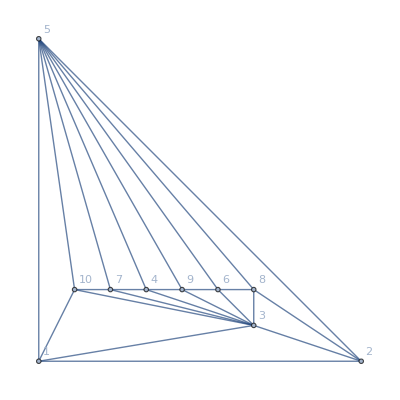

```mathematica
Graph[ReadGrof[305],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

```mathematica
With[
{size=7},
Select[Table[k,{k,StartMpg[[size]],EndMPG[[size]]}],ChromaticPolynomial[ReadGrof[#],3]>0&]
]
```

{817,1349}

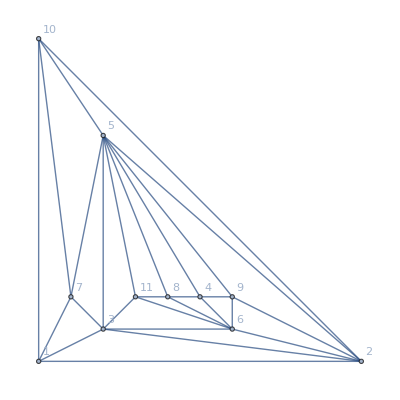

```mathematica
Graph[ReadGrof[817],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

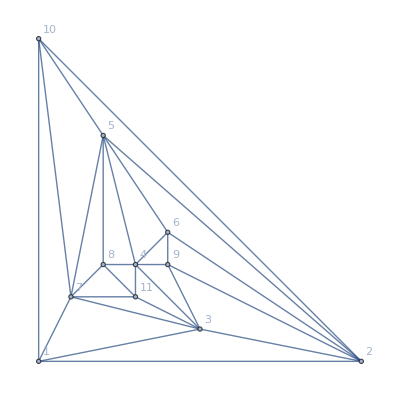

```mathematica
Graph[ReadGrof[1349],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

```mathematica
EndMPG[[8]]
```

9150

```mathematica
With[
{size=8},
Select[Table[k,{k,StartMpg[[size]],EndMPG[[size]]}],ChromaticPolynomial[ReadGrof[#],3]>0&]
]
```

{}

```mathematica
With[
{size=9},
Select[Table[k,{k,StartMpg[[size]],EndMPG[[size]]}],ChromaticPolynomial[ReadGrof[#],3]>0&]
]
```

$Aborted

```mathematica
Graph[ReadGrof[1349],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

```mathematica
Table[ChromaticPolynomial[JacobsThalGraph[k],3],{k,2,10,2}]
```

{6,6,6,6,6}

```mathematica
TableForm[Map[Factor[#/((-2+x) (-1+x) x )]&,Select[Keys[chromis],(#/.x->3)≠0&]]]
```

-32+29 x-9 x^2+x^3
-332+498 x-303 x^2+94 x^3-15 x^4+x^5
(-32+29 x-9 x^2+x^3)^2
-3728+7603 x-6734 x^2+3371 x^3-1034 x^4+195 x^5-21 x^6+x^7
-3152+6787 x-6301 x^2+3269 x^3-1025 x^4+195 x^5-21 x^6+x^7
(-32+29 x-9 x^2+x^3) (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)
13360-30250 x+30418 x^2-17818 x^3+6674 x^4-1641 x^5+259 x^6-24 x^7+x^8
(-32+29 x-9 x^2+x^3)^3
-45860+115520 x-131190 x^2+88471 x^3-39164 x^4+11829 x^5-2441 x^6+332 x^7-27 x^8+x^9
-41108+106556 x-124125 x^2+85487 x^3-38450 x^4+11737 x^5-2436 x^6+332 x^7-27 x^8+x^9
-36212+96992 x-116339 x^2+82102 x^3-37620 x^4+11628 x^5-2430 x^6+332 x^7-27 x^8+x^9
-29012+81860 x-102981 x^2+75761 x^3-35913 x^4+11381 x^5-2415 x^6+332 x^7-27 x^8+x^9
(-32+29 x-9 x^2+x^3) (-3728+7603 x-6734 x^2+3371 x^3-1034 x^4+195 x^5-21 x^6+x^7)
142984-405828 x+524191 x^2-406656 x^3+210265 x^4-75855 x^5+19366 x^6-3459 x^7+414 x^8-30 x^9+x^10
(-332+498 x-303 x^2+94 x^3-15 x^4+x^5)^2
164944-452040 x+565859 x^2-427540 x^3+216554 x^4-76994 x^5+19481 x^6-3464 x^7+414 x^8-30 x^9+x^10
(-32+29 x-9 x^2+x^3) (-3152+6787 x-6301 x^2+3269 x^3-1025 x^4+195 x^5-21 x^6+x^7)
134344-387036 x+506623 x^2-397471 x^3+207351 x^4-75291 x^5+19304 x^6-3456 x^7+414 x^8-30 x^9+x^10
(-32+29 x-9 x^2+x^3)^2 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)
-413432+1325781 x-1947653 x^2+1732059 x^3-1037226 x^4+439690 x^5-134801 x^6+29928 x^7-4722 x^8+505 x^9-33 x^10+x^11
-455048+1429413 x-2060721 x^2+1802711 x^3-1064903 x^4+446656 x^5-135902 x^6+30028 x^7-4726 x^8+505 x^9-33 x^10+x^11
(-32+29 x-9 x^2+x^3) (13360-30250 x+30418 x^2-17818 x^3+6674 x^4-1641 x^5+259 x^6-24 x^7+x^8)
-574280+1713885 x-2358774 x^2+1982087 x^3-1132826 x^4+463252 x^5-138461 x^6+30256 x^7-4735 x^8+505 x^9-33 x^10+x^11